# comparing cutoff and smearing

## part two

## set some parameters

```mathematica
α=1;
```

```mathematica
numSteps=200;
```

```mathematica
Ω=1;
```

#### set values of σ;write σ in terms ofσ_0~10^-4/Ω

```mathematica
σ0:=10^-4/Ω;
```

```mathematica
(*use these values for calculations*)
numSteps=200;
σMin=0.1 σ0;  σMax=2 σ0;  σStepSize=Abs[σMin-σMax]/numSteps;
σValues=Table[σ,{σ,σMin,σMax,σStepSize}];
```

```mathematica
(*then plot <g|ρ|g> versus σNorm=σ/Subscript[σ, 0]*)
σNormValues=σValues/σ0;
```

```mathematica
clear[λ];
```

## the smearing functions

```mathematica
fL[x_,σ_]:=σ/π 1/(x^2+σ^2)
ftilL[k_,σ_]:=FourierTransform[fL[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

```mathematica
ftilL[k,σ]
```

ⅇ^(-k σ) (ⅇ^(2 k σ) HeavisideTheta[-k]+HeavisideTheta[k])

```mathematica
fG[x_,σ_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftilG[k_,σ_]:=FourierTransform[fG[x,σ],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

```mathematica
ftilG[k,σ]
```

ⅇ^(-1/4 k^2 σ^2)

## the switching function

```mathematica
chiT1[t_]:=1/(r+T)1/2*(1+Cos[π/r(t+T/2)])
chiT2[t_]:=1/(r+T)
chiT3[t_]:=1/(r+T)1/2*(1+Cos[π/r(t-T/2)])
```

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ]:=tpInt1[t,k]=NIntegrate[chiT1[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T-r,t}]
```

```mathematica
tInt1[k_?NumericQ]:=tInt1[k]=α*NIntegrate[chiT1[t] tpInt1[t,k],
{t,-T-r,-T}]
```

### the second interval

```mathematica
tpInt2[t_,k_]:=Integrate[chiT2[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T,t}]
```

```mathematica
tInt2[k_]:=α*Integrate[chiT2[t] tpInt2[t,k],
{t,-T,T}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ]:=tpInt3[t,k]=NIntegrate[chiT3[tp]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,T,t}]
```

```mathematica
tInt3[k_?NumericQ]:=tInt3[k]=α*NIntegrate[chiT3[t] tpInt3[t,k],
{t,T,T+r}]
```

## the k integrand

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
kIntegrandG[k_,σ_]:=-1/π ⅇ^(-ε/2*k)*k*ftilG[k,σ]^2*(tInt1[k]+tInt2[k]+tInt3[k])
```

```mathematica
kIntegrandL[k_,σ_]:=-1/π ⅇ^(-ε/2*k)*k*ftilL[k,σ]^2*(tInt1[k]+tInt2[k]+tInt3[k])
```

## the numerical transition probability

```mathematica
T=4;r=0.2;Ω=1;
```

### exp cutoff

```mathematica
ε=1/(5 Ω);
```

```mathematica
pExpG=Table[α+λ^2*NIntegrate[kIntegrandG[k,σ],{k,0,∞}],{σ,σMin,σMax,σStepSize}];
```

```mathematica
pExpG10σ=α+λ^2*NIntegrate[kIntegrandG[k,10 σ0],{k,0,∞}]
```

1-0.229317 λ^2

```mathematica
pExpL=Table[α+λ^2*NIntegrate[kIntegrandL[k,σ],{k,0,∞}],{σ,σMin,σMax,σStepSize}];
```

```mathematica
pExpL10σ=α+λ^2*NIntegrate[kIntegrandL[k,10 σ0],{k,0,∞}]
```

1-0.228324 λ^2

### sharp cutoff

```mathematica
ε=0;  cutoff=5*Ω;
```

```mathematica
pSharpG=Table[α+λ^2*NIntegrate[kIntegrandG[k,σ],{k,0,cutoff}],{σ,σMin,σMax,σStepSize}];
```

```mathematica
pSharpG10σ=α+λ^2*NIntegrate[kIntegrandG[k,10 σ0],{k,0,cutoff}]
```

1-0.238848 λ^2

```mathematica
pSharpL=Table[α+λ^2*NIntegrate[kIntegrandL[k,σ],{k,0,cutoff}],{σ,σMin,σMax,σStepSize}];
```

```mathematica
pSharpL10σ=α+λ^2*NIntegrate[kIntegrandL[k,10 σ0],{k,0,cutoff}]
```

1-0.238224 λ^2

## plot

```mathematica
λ=0.1;
```

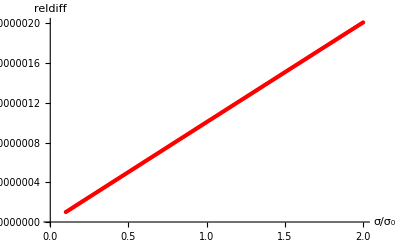

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpG-pExpL]/pExpG}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Red},
PlotLabel->Style["",FontSize->16]]
```

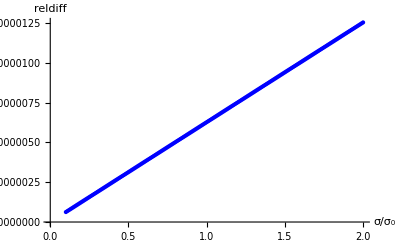

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pSharpG-pSharpL]/pSharpG}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Blue},
PlotLabel->Style["",FontSize->16]]
```

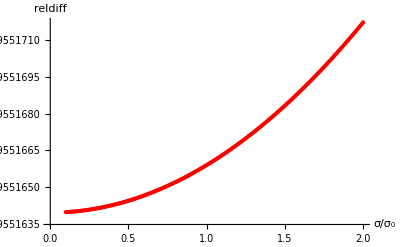

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpG-pSharpG]/pSharpG}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Red},
PlotLabel->Style["",FontSize->16]]
```

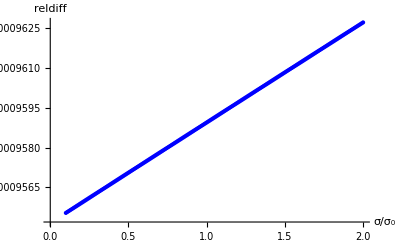

```mathematica
ListPlot[{Transpose[{σNormValues,Abs[pExpL-pSharpL]/pSharpL}]},
AxesLabel->{σ/Subscript[σ, 0],reldiff},
PlotStyle->{Blue},
PlotLabel->Style["",FontSize->16]]
```

## σ stuff

```mathematica
σNormValues[[1]]
```

0.1

```mathematica
σNormValues[[201]]
```

2.

### gaussian smear, sharp cutoff

```mathematica
Abs[pSharpG[[201]]-pSharpG[[1]]]/pSharpG[[1]]
```

1.08996×10^-10

```mathematica
Abs[pSharpG10σ-pSharpG[[1]]]/pSharpG[[1]]
```

2.73144×10^-9

### gaussian smear, exp cutoff

```mathematica
Abs[pExpG[[201]]-pExpG[[1]]]/pExpG[[1]]
```

8.78182×10^-10

```mathematica
Abs[pExpG10σ-pExpG[[1]]]/pExpG[[1]]
```

2.20042×10^-8

### lorentzian smear, sharp cutoff

```mathematica
Abs[pSharpL[[201]]-pSharpL[[1]]]/pSharpL[[1]]
```

1.19135×10^-6

```mathematica
Abs[pSharpL10σ-pSharpL[[1]]]/pSharpL[[1]]
```

6.1989×10^-6

### lorentzian smear, exp cutoff

```mathematica
Abs[pExpL[[201]]-pExpL[[1]]]/pExpL[[1]]
```

1.90838×10^-6

```mathematica
Abs[pExpL10σ-pExpL[[1]]]/pExpL[[1]]
```

9.87508×10^-6

## save this time valuable shit

```mathematica
basePath="C:/Users/Public/Documents/emma/udw-detector-shape/Cosine Trap Switching/";
```

```mathematica
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pSharpL.csv",pSharpL];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pSharpG.csv",pSharpG];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pExpL.csv",pExpL];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pExpG.csv",pExpG];
```